```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=32;
Ly=32;
A=Lx*Ly;
```

```mathematica
B=1/Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,100]
```

{-3.14159,-3.07876,-3.01593,-2.9531,-2.89027,-2.82743,-2.7646,-2.70177,-2.63894,-2.57611,-2.51327,-2.45044,-2.38761,-2.32478,-2.26195,-2.19911,-2.13628,-2.07345,-2.01062,-1.94779,-1.88496,-1.82212,-1.75929,-1.69646,-1.63363,-1.5708,-1.50796,-1.44513,-1.3823,-1.31947,-1.25664,-1.19381,-1.13097,-1.06814,-1.00531,-0.942478,-0.879646,-0.816814,-0.753982,-0.69115,-0.628319,-0.565487,-0.502655,-0.439823,-0.376991,-0.314159,-0.251327,-0.188496,-0.125664,-0.0628319,0.,0.0628319,0.125664,0.188496,0.251327,0.314159,0.376991,0.439823,0.502655,0.565487,0.628319,0.69115,0.753982,0.816814,0.879646,0.942478,1.00531,1.06814,1.13097,1.19381,1.25664,1.31947,1.3823,1.44513,1.50796,1.5708,1.63363,1.69646,1.75929,1.82212,1.88496,1.94779,2.01062,2.07345,2.13628,2.19911,2.26195,2.32478,2.38761,2.45044,2.51327,2.57611,2.63894,2.70177,2.7646,2.82743,2.89027,2.9531,3.01593,3.07876,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

101

```mathematica
(** Mixed boundary **)
```

```mathematica
bb = Import["WholeCrystalLandauLevels32x32LineUp+8LineDn-6WSM3.dat"]
```

{{-3.14159,-4.98433},{-3.14159,-4.98429},{-3.14159,-4.98106},{-3.14159,-4.98048},{-3.14159,-4.96383},{-3.14159,-4.96194},{-3.14159,-4.95868},{-3.14159,-4.95844},{-3.14159,-4.94789},{-3.14159,-4.94652},{-3.14159,-4.9313},206826,{3.14159,4.93724},{3.14159,4.95253},{3.14159,4.95391},{3.14159,4.9645},{3.14159,4.96475},{3.14159,4.96802},{3.14159,4.96991},{3.14159,4.98666},{3.14159,4.98724},{3.14159,4.99048},{3.14159,4.99052}}
 |  |  |  |

```mathematica
Show[ListPlot[bb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.03]],AxesLabel-> {"kz","Energy"},Frame-> True]
```

-Graphics-

```mathematica
Plot1=Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],Axes->{True,False}]
```

-Graphics-

```mathematica
(** Plots for m = 4 **)
```

```mathematica
Dimensions[bb]
```

{206848,2}

```mathematica
Dimensions[kzVector][[1]]*2*A
```

206848

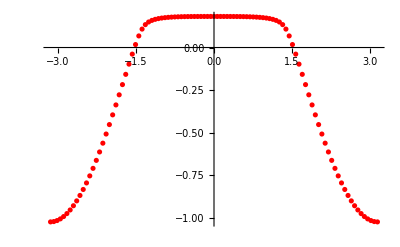

```mathematica
LandauLevelMixed1 = {};
Do[LandauLevelMixed1 = Append[LandauLevelMixed1,bb[[A -3+ n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed1,PlotStyle->Red]]
```

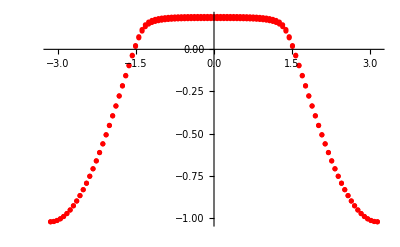

```mathematica
LandauLevelMixed11 = {};
Do[LandauLevelMixed1 = Append[LandauLevelMixed1,bb[[A -2+ n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed1,PlotStyle->Red]]
```

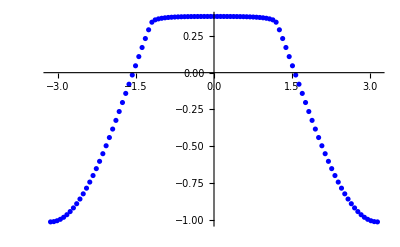

```mathematica
LandauLevelMixed2 = {};
Do[LandauLevelMixed2 = Append[LandauLevelMixed2,bb[[A + n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed2,PlotStyle->Blue]]
```

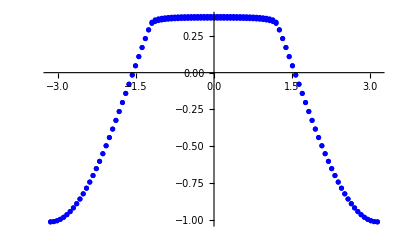

```mathematica
LandauLevelMixed22 = {};
Do[LandauLevelMixed2 = Append[LandauLevelMixed2,bb[[A -1+ n *2*A]]],{n,0,Dimensions[kzVector][[1]]-1}];
Show[ListPlot[LandauLevelMixed2,PlotStyle->Blue]]
```

```mathematica
Show[Plot1,ListPlot[LandauLevelMixed1,PlotStyle->Red],ListPlot[LandauLevelMixed2,PlotStyle->Blue],
ListPlot[LandauLevelMixed11,PlotStyle->Red],ListPlot[LandauLevelMixed22,PlotStyle->Blue],
ImageSize-> 800,Frame-> True,
FrameLabel-> {"k_z","E"},BaseStyle-> 28,RotateLabel->False,
FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks->{{{-π+0.01,"-π"},{-π/2,"-π/2"},{0,"0"},{π/2,"π/2"},{π-0.01,"π"}},{{-2,"-2"},{-1,"-1"},{0,"0"},{1,"1"},{2,"2"}},None,None}]
```

-Graphics-

```mathematica
(** Plot for m = 4, 32x32 WSM3 **)
```

```mathematica
(** Plot for m = 0, 32x32 WSM1 **)
```